```mathematica
ClearAll[MStar, LStar, L,alpha,ω,Ls, deinemudda]
```

```mathematica
(* Subscript[Ω, n]=Surface of n-Sphere. *)
Ω[n_] = 2*Pi^((n+3)/2) / ( Gamma[(n+3)/2]);
ω[n_]=Ω[n]/Ω[0];
α[n_] = (3+n)/(Log[(2+n)/ω[n]])* Log[(3+n)/2];
LStar[n_]=(1+n)^(-1/α[n])
MStar[n_] = 1 / LStar[n];
GStar[n_] = LStar[n]^2;
```

(1+n)^(-Log[2 (2+n) π^(1+1/2 (-3-n)) Gamma[(3+n)/2]]/((3+n) Log[(3+n)/2]))

```mathematica
maxN = 7; (* Welches n=D-4 maximal betrachten *)
```

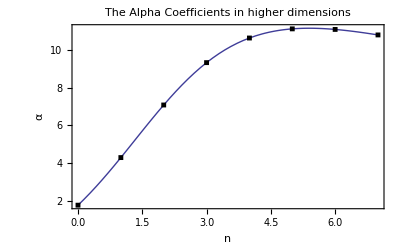

```mathematica
(* Plot α *)
pa=Plot[α[n], {n,0,maxN}, AxesLabel-> {n,α},PlotLabel-> "The Alpha Coefficients in higher dimensions",Frame->True];
pad = DiscretePlot[α[n],{n,0,maxN},Filling-> None,PlotMarkers->{Graphics[{Black,Rectangle[]}],Small}];
Show[pa,pad]
```

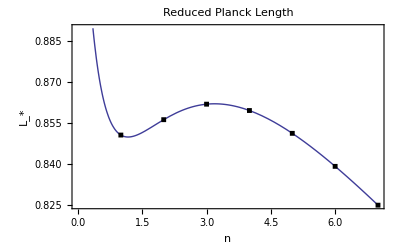

```mathematica
(* Plot LStar *)
pL=Plot[LStar[n], {n,0,maxN}, AxesLabel-> {n,SubStar[L]},PlotLabel-> "Reduced Planck Length",Frame->True];
pLd = DiscretePlot[LStar[n],{n,0,maxN},Filling-> None,PlotMarkers->{Graphics[{Black,Rectangle[]}],Small}];
Show[pL,pLd]
```

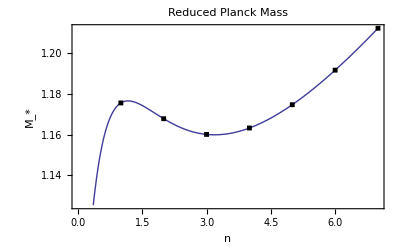

```mathematica
(* Plot MStar *)
pM = Plot[MStar[n],{n,0,maxN},
AxesLabel->{n,SubStar[M]}, PlotLabel-> "Reduced Planck Mass",Frame->True ];
pMd = DiscretePlot[MStar[n],{n,0,maxN},Filling-> None,PlotMarkers->{Graphics[{Black,Rectangle[]}],Small}];
Show[pM,pMd]
```

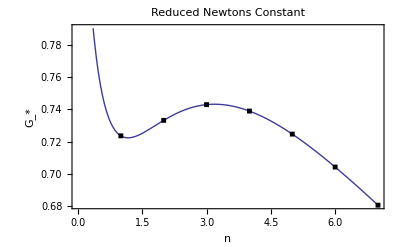

```mathematica
(* Plot GStar *)
pG = Plot[GStar[n],{n,0,maxN},
AxesLabel->{n,SubStar[G]}, PlotLabel-> "Reduced Newtons Constant",Frame->True ];
pGd = DiscretePlot[GStar[n],{n,0,maxN},Filling-> None,PlotMarkers->{Graphics[{Black,Rectangle[]}],Small}];
Show[pG,pGd]
```

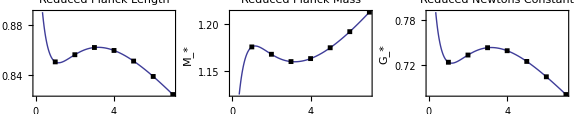

```mathematica
GraphicsGrid[{{Show[pL,pLd],Show[pM,pMd], Show[pG,pGd]}},ImageSize -> Large]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["table-graphs.pdf",%%,"PDF"]
```

table-graphs.pdf

```mathematica
(* N[z,n] gibt Zahl inkl Vorkomma auf n Stellen an.
Nk gibt Zahl auf n Nachkommastellen an *)
Nk[zahl_,n_] := N[Round[zahl*10^n] / 10^n];
```

```mathematica
Grid[{
Prepend[Table[n, {n,0,maxN}],"n"],
Prepend[Nk[Table[α[n], {n,0,maxN}],3], "α"],
Prepend[Nk[Table[LStar[n],{n,0,maxN}],3],"L_*"],
Prepend[Nk[Table[MStar[n], {n,0,maxN}],3], "M_*"],
Prepend[Nk[Table[GStar[n], {n,0,maxN}],3], "G_*"]
},Frame->All]
```

n | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
α | 1.755 | 4.285 | 7.081 | 9.333 | 10.642 | 11.128 | 11.098 | 10.805
L_* | 1. | 0.851 | 0.856 | 0.862 | 0.86 | 0.851 | 0.839 | 0.825
M_* | 1. | 1.176 | 1.168 | 1.16 | 1.163 | 1.175 | 1.192 | 1.212
G_* | 1. | 0.724 | 0.733 | 0.743 | 0.739 | 0.725 | 0.704 | 0.681